```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]

ClearAll;

workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/mul_helion_test/results/";
SetDirectory[workingdirectory]
e0=ReadList["../E0.dat",Number][[1]];
hb=197.32858;
Mnucl=(938.2796+939.5731)/2.;
threshold=10^-4;

λi=1;λf=1; (* in/outgoing-photon polarization = ±1 ? *)
nu=0;nup=0; (* ν=0 ↔ electric multipoles *)
Ll=1;
Llp=1;
Iini=0.5;Ifin=0.5;

multipolarity=1;
parity="-";
Js={0.5};
mJs=Range[-#,#,1]&/@Js;

σI=5.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];

kRange=ReadList["../kRange.dat",Number];
ks=Table[kRange[[2]]+n kRange[[3]],{n,0,kRange[[1]]-1}];
k0=0.0;k1=100;dK=0.5;
kσ=Range[k0,k1,dK];
momIndex=1;mom=ks[[Min[momIndex,Length[ks]]]];(* to approximate Subscript[D, 1], always use the smallest momentum *)
Print["k = ",N[mom]," MeV ,   B(^3He) = ",N[e0]];
basisdims=Table[Sort[DeleteDuplicates[ToExpression[StringSplit[#,"-"][[-1]]]&/@Select[FileNames[],StringContainsQ[#,"LIT_SOURCE_"<>ToString[J]<>"^"<>parity]&]]],{J,Js}];
Print["Basis dimensions: ",basisdims]

nB=194;
Print[Style["ECCE! dim_work="<>ToString[basisdims[[#]][[Min[nB,Length[basisdims[[#]]]]]]&/@Range[Length[Js]]],12,Red]]
```

/home/kirscher/kette_repo/ComptonLIT/mul_helion_test/results

k = 0.001 MeV ,   B(^3He) = 1.0758

Basis dimensions: {{5,10,15,20,25,30}}

ECCE! dim_work={30}

#### Naive approach (pseudo-inverse solution)

JbasisDim = 30   :  ./LIT_SOURCE_0.5^-_mJ-0.5_MUL1_bv_1-30

JbasisDim = 30   :  ./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-30

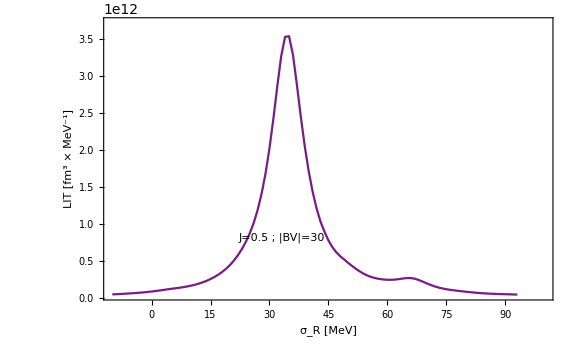

```mathematica
SetSharedVariable[LITs,LITsBasdi,testfu]
LITs={};LITsBasdi={};
Do[
nB=Min[nB,Length[basisdims[[nJ]]]];
lbd=basisdims[[nJ]][[nB]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
genevham=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normev=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
genevhamN=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normevN=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

testfu=0;
Do[
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
Print["JbasisDim = ",JbasisDim,"   :  ",file];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True][[momIndex]];
inhomo=renorm.inhomo;

testfu+=(Function[{σR},Block[{mm,coeff},
mm=PseudoInverse[ham-(σR-σI ⅈ) norm,Tolerance->threshold];
coeff=mm.inhomo;{σR,Chop[Conjugate[coeff].norm.coeff]}]]/@σRs)[[All,2]];

,{mJ,mJs[[nJ]][[1]],mJs[[nJ]][[-1]]}];

AppendTo[LITsBasdi,lbd];
AppendTo[LITs,Transpose[{σRs,(-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) testfu}]];

,{nJ,1,Length[Js]}]
pltmaxcfg=Length[LITs];
peakmax=Max[Table[Max[Re[LITs[[nn]]][[All,2]]],{nn,pltmaxcfg}]];
peakmin=Min[Table[Min[Re[LITs[[nn]]][[All,2]]],{nn,pltmaxcfg}]];
ListPlot[Re[LITs],Joined->True,Frame->True,PlotRange->{{σRs[[1]],σRs[[-1]]},{1.05 peakmin,1.05 peakmax}},FrameLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/(Length[LITs])]]]&[Floor[i-1,1]+1],{i,1,Length[LITs]}],PlotLabels->Placed["J="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[LITsBasdi[[#]]]&/@Table[n,{n,Length[Js]}],Top],ImageSize->Large]
```

#### Alternative approach (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

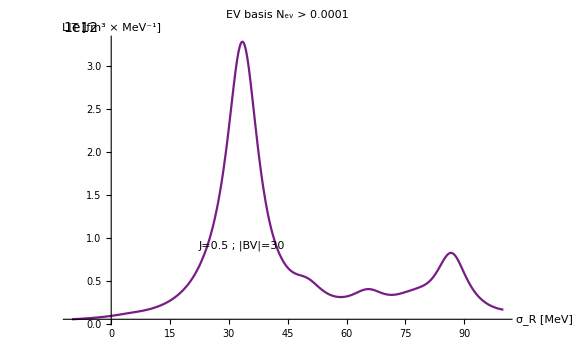

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
NielsLITs={};
LITcompos={};

Do[
nB=Min[nB,Length[basisdims[[nJ]]]];
lbd=basisdims[[nJ]][[nB]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];

testfu=0;testcompo={};
Do[

file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True][[momIndex]];

Clear[normreg];normreg[threshold_]:=Block[
{es=Eigensystem[norm],μ,transf,μs,Or},
{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];
If[Dimensions[μ]<Dimensions[es[[1]]],
{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];
,{μs,Or}={{},{}}];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}];
Clear[decompose];
decompose[threshold_]:= Block[{Oμ,Or,μs,oλs,otrf},
{Oμ,Or,μs}=normreg[threshold];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];{λs,(-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) trf.(Transpose[Oμ].inhomo)}
];
Clear[litcomp,litshow];
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@(((-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) (#[[2]])^2/((#[[1]]-σRe)^2+σIm^2))&/@λscf)];
litshow[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},{#[[1]],Abs[#[[2]]]^2}&/@λscf];
testfu+=Evaluate[litcomp[threshold]/.{σIm->σI}];
tmps=Transpose[decompose[100]];
testcompo=AppendTo[testcompo,Re[tmps]];
,{mJ,mJs[[nJ]][[1]],mJs[[nJ]][[-1]]}];
AppendTo[NielsLITs,testfu];
AppendTo[LITcompos,Flatten[testcompo,1]];

,{nJ,1,Length[LITs]}];

Show[
Plot[NielsLITs,{σRe,-10,100},PlotRange->{Automatic,Full},
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->Large,PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[LITs]]]]&[Floor[i-1,1]+1],{i,1,Length[LITs]}],PlotLabels->Placed["J="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[LITsBasdi[[#]]]&/@Table[n,{n,Length[Js]}],Top],ImageSize->Large]
(*,ListLinePlot[Function[{σR},Block[{mm,coeff},mm=pseudoinverse[th,σR,σI];coeff=mm.inhomo;{σR,Re[Conjugate[coeff].norm.coeff]}]]/@σRs,PlotRange->All,PlotStyle->Red,PlotLegends->{"Pseudo inverse with thres = "<>ToString[N[th],TraditionalForm]},ImageSize->Large]*)
]
```

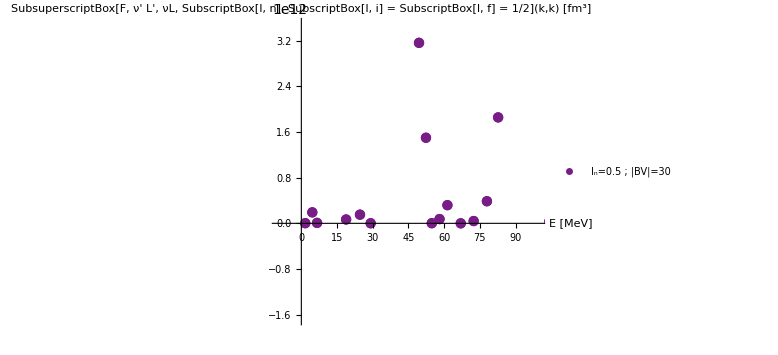

```mathematica
maxi=1.05 Max[Table[Max[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
mini=0.95 Min[Table[Min[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
λψm=LITcompos;
strengthfunctionBare=({#[[1]],(*Sign[#[[2]]]*) (#[[2]]^2)})&/@#&/@λψm;
ListPlot[strengthfunctionBare,Joined->False,PlotRange->{{-10,100},{-mini^2,maxi^2}},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[LITs]]]]&[Floor[i-1,1]+1],{i,1,Length[LITs]}],PlotLegends->{"I_n="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[LITsBasdi[[#]]]&/@Table[n,{n,Length[Js]}]},ImageSize->Large]
```

```mathematica
StrengthFLorentz[E_,eps_,psiSQ_,lamM_]:=Pi^-1 psiSQ^2 eps/((E-lamM)^2+eps^2);
StrengthFGauss[E_,eps_,psiSQ_,lamM_]:=(*Sign[psiSQ]*) psiSQ^2 Exp[-(E-lamM)^2/(4 eps)]/(2 Sqrt[eps Pi]);
StrengthFSinc[E_,eps_,psiSQ_,lamM_]:=(Pi (E-lamM))^-1 psiSQ^2 Sin[(E-lamM)/eps];
StrengthFBessel[E_,eps_,psiSQ_,lamM_]:=psiSQ^2 BesselJ[1/eps,(E-lamM+1)/eps]/eps;
StrengthFLaguerre[E_,eps_,psiSQ_,lamM_,nn_]:=psiSQ^2/Sqrt[Pi eps] Abs[Exp[-eps^-1 (E-lamM)^2]LaguerreL[nn,2 (E-lamM)/eps]];
```

ϵ→0 ⇒ peak amplitude → "truth" ⇒ σ-peak→"truth" but  no info on E ∩ EV=0
on the other hand
 ϵ≈σ_I ⇒ significant loss of "strength"

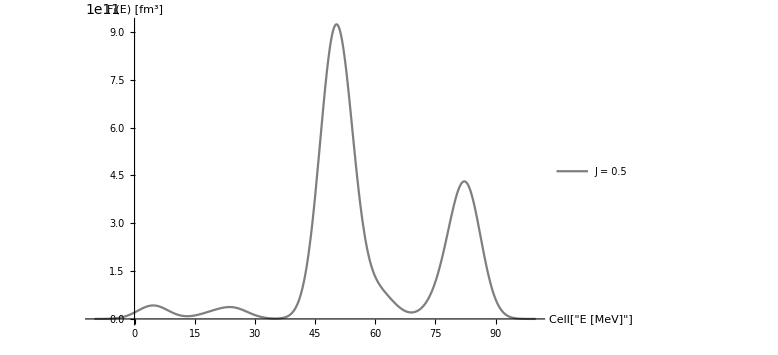

```mathematica
SetSharedVariable[z]
epsi=7.2;
evth=100;
z=List[];
Do[
ploty=Plot[Total[StrengthFGauss[x,epsi,#1[[2]],#1[[1]]]&/@Select[λψm[[nj]],#[[1]]<evth&]],{x,-10,Min[evth,100]},PlotRange->Full,AxesLabel->{"Cell["E [MeV]",ExpressionUUID->"75691706-e9a7-4580-b0d0-72e5fe7f0e74"]","F_j(E) [fm^3]"},ImageSize->Large,PlotStyle->(ColorData[7,"ColorList"][[nj]]),PlotLegends->{"J = "<>ToString[Js[[nj]]]}];
AppendTo[z,ploty];
,{nj,Length[Js]}
]
Show[z,PlotRange->All]
```

#### Adapt the inspired (see above) and a randomly chosen Lorentz-transformed Lorentz basis to the model LIT and compare the thereby reconstructed cross section with the original data

```mathematica
hat[l_]:=Sqrt[2 l+1];
ILanaPlus[sr_,si_,a_,b_,eth_,c_,sgn_]:=sgn c^2/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)]);
LorentzPlus[e_,a_,b_,eth_,c_,sgn_]:=HeavisideTheta[e-eth] sgn c^2/((a-e)^2+b^2);
```

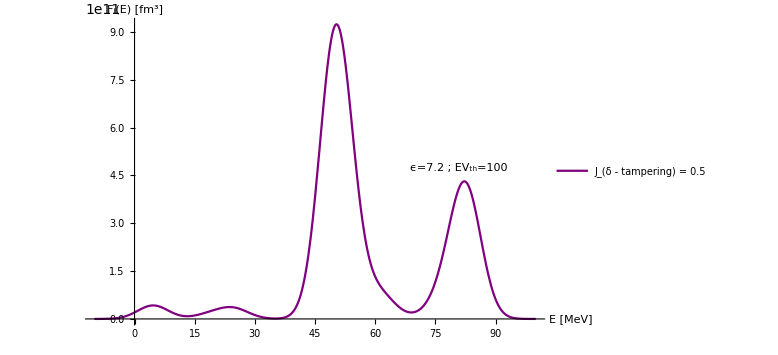
-Graphics- |  | -Graphics-

```mathematica
plotlistRESPONSEs2={};
For[nJ=1,nJ≤Length[LITs],nJ++,
plotRESPONSE2=Total[StrengthFGauss[e2,epsi,#[[2]],#[[1]]]&/@Select[λψm[[nJ]],#[[1]]<evth&]];
(*plotRESPONSE2=Total[StrengthFLaguerre[e2,epsi,#[[2]],#[[1]],0]&/@Select[λψm[[nJ]],#[[1]]<evth&]]*);
plotlistRESPONSEs2=AppendTo[plotlistRESPONSEs2,plotRESPONSE2];
];

labeljlit2=("J_(δ - tampering) = "<>ToString[#])&/@Js;
labeljlit=("J = "<>ToString[#])&/@Js;
Grid[{{
ListLinePlot[LITs,PlotStyle->{Large,Red},PlotRange->Full,LabelStyle->Directive[Larger],PlotLegends->labeljlit,ImageSize->Large,AxesLabel->{"σ [MeV]","L_j(σ) [fm^3 × MeV^-1]"}],
,
Plot[plotlistRESPONSEs2,{e2,-10,100},PlotRange->{{-10,100},Full},PlotLegends->labeljlit2,PlotStyle->{Red,Purple},AxesLabel->{"E [MeV]","F_j(E) [fm^3]"},PlotLabels->Placed["ϵ="<>ToString[epsi]<>" ; EV_th="<>ToString[evth],Right],LabelStyle->Directive[Larger],ImageSize->Large]
}}]
```

#### basis-adaptation method

loc_min = 1.  loc_max = 31.5

loc_th = 5.  peak_th = 0.0657555

loc_min = 1.  loc_max = 31.5

loc_th = 5.  peak_th = 0.128168

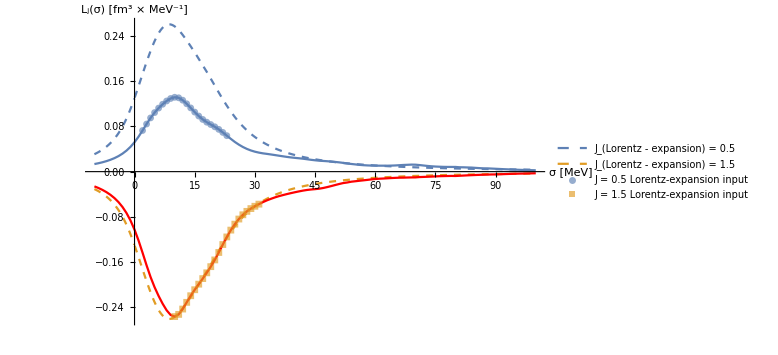
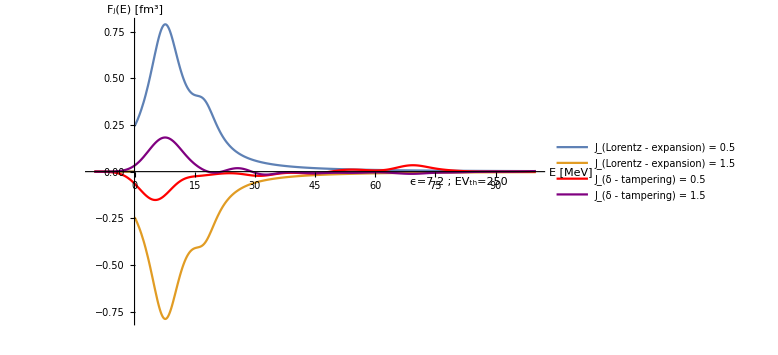
-Graphics- | -Graphics-

```mathematica
(* Determine the data range -- left of peak -- used for the Lorentzian expansion *)
plotlistRESPONSEs={};plotlistLITs={};datacrossLITs={};

For[nJ=1,nJ≤Length[LITs],nJ++,
dmax=Max[Abs[LITs[[nJ]][[All,2]]]];
posdatamax=Position[Abs[LITs[[nJ]]],dmax][[1]][[1]];
datamax={LITs[[nJ]][[posdatamax]][[1]],Re[LITs[[nJ]][[posdatamax]][[2]]]};
posmax=posdatamax;
While[Re[LITs[[nJ]][[posmax]][[2]]]>0.6 datamax[[2]],
posmax--;
];
posdatasig=posmax;
ub=LITs[[nJ]][[-1]][[1]];
lb=LITs[[nJ]][[1]][[1]];
randdim=25;
e0=-7.0;
peakpercentdiff=0.5;
locpercentdiff=0.5;
expansioninputL={posdatasig,posdatamax+posdatasig};
smin=lb;smax=ub;
dataCrossLit=LITs[[nJ]][[expansioninputL[[1]];;expansioninputL[[2]]]];
peakth=Abs[datamax[[2]]] peakpercentdiff;
locth=Abs[datamax[[1]]] locpercentdiff;

locMin=datamax[[1]] 0.1;locMax=datamax[[1]] 3.15;
widthMin=3.9;widthMax=13.9;

Print["loc_min = "<>ToString[locMin]<>"  loc_max = "<>ToString[locMax]];
Print["loc_th = ",locth,"  peak_th = ",peakth];

peakmatch=False;

While[peakmatch==True,

lorentzbasplus=Table[{RandomReal[{locMin,locMax}],RandomReal[{widthMin,widthMax}],0.0},{n,randdim}];


brutedimp=Length[lorentzbasplus];
Clear[abrute];coeffsb=Array[abrute,brutedimp];

LinearLorentzModelb=Sum[ILanaPlus[sigmaR,σI,lorentzbasplus[[i]][[1]],lorentzbasplus[[i]][[2]],lorentzbasplus[[i]][[3]],coeffsb[[i]],Sign[datamax[[2]]]],{i,brutedimp}];

modelLorentzABCpm=FindFit[Re[dataCrossLit],LinearLorentzModelb,coeffsb,sigmaR,MaxIterations->2000,PrecisionGoal->12,AccuracyGoal->12,Method->Automatic];

optPOSsol=Map[Rule[#[[1]],If[Abs[#[[2]]]>10^-12,Abs[#[[2]]],0.0]]&,modelLorentzABCpm];

expan[x_]:=LinearLorentzModelb/.optPOSsol/.sigmaR->x;
modmax=Maximize[expan[eee],eee];

peakdiff=Abs[modmax[[1]]-datamax[[2]]];
	     locdiff=Abs[modmax[[2]][[1]][[2]]-datamax[[1]]];

If[((peakdiff<peakth)&&(locdiff<locth)),{peakmatch=True;optPOSsol;lorentzbasplus},peakmatch=False];

];
(*Print["Fit_max (J="<>ToString[jlit[[nJ]]]<>") = "<>ToString[Maximize[expan[e],e],TraditionalForm]<>"  peakth="<>ToString[peakth,TraditionalForm]];*)

(*i,i--];*)
cycl=Table[Rule[n,{n+1}],{n,Length[litfitList]-1}];
plotRESPONSE=(Sum[LorentzPlus[e2,lorentzbasplus[[m]][[1]],lorentzbasplus[[m]][[2]],lorentzbasplus[[m]][[3]],coeffsb[[m]],Sign[datamax[[2]]]],{m,brutedimp}])/.optPOSsol;
plotLIT=Sum[ILanaPlus[sigmaR,σI,lorentzbasplus[[i]][[1]],lorentzbasplus[[i]][[2]],lorentzbasplus[[i]][[3]],coeffsb[[i]],Sign[datamax[[2]]]],{i,brutedimp}]/.optPOSsol/.sigmaR->x;

plotlistLITs=AppendTo[plotlistLITs,plotLIT];plotlistRESPONSEs=AppendTo[plotlistRESPONSEs,plotRESPONSE];
datacrossLITs=AppendTo[datacrossLITs,dataCrossLit];

];
labeljlitFit=("J = "<>ToString[#]<>"  Lorentz-expansion input")&/@Js;
labeljlit=("J_(Lorentz - expansion) = "<>ToString[#])&/@Js;
labeljlit2=("J_(δ - tampering) = "<>ToString[#])&/@Js;

Grid[{{
Show[
Plot[plotlistLITs,{x,smin,smax},PlotStyle->{Dashed},PlotLegends->labeljlit,PlotRange->Full,PlotPoints->40,ImageSize->Large(*,Filling->cycl*),AxesLabel->{"σ [MeV]","L_j(σ) [fm^3 × MeV^-1]"},LabelStyle->Directive[Larger]],
ListLinePlot[LITs,PlotStyle->{Large,Red},PlotRange->Full,LabelStyle->Directive[Larger]],
ListPlot[datacrossLITs,PlotStyle->{Opacity[0.65]},PlotMarkers->{Automatic,Small},PlotLegends->labeljlitFit,LabelStyle->Directive[Larger]]
],
Show[
Plot[plotlistRESPONSEs,{e2,-10,100},PlotRange->Full,PlotLegends->labeljlit,AxesLabel->{"E [MeV]","F_j(E) [fm^3]"},
ImageSize->Large,LabelStyle->Directive[Larger]],
Plot[plotlistRESPONSEs2,{e2,-10,100},PlotRange->{{-10,100},Full},PlotLegends->labeljlit2,PlotStyle->{Red,Purple},PlotLabels->Placed["ϵ="<>ToString[epsi]<>" ; EV_th="<>ToString[evth],Right]]
]}}]
```

#### strength functions from partial strength functions

F_((ν'L'νL)J)^(I_f I_i)(k,k;E)=(E-E_0)^2∑_I_n {L
I_fL'
I_iJ
I_n} F_ν'L'νL^(I_f I_i;I_n)(k,k;E)
[fm^3·MeV^2]               [MeV^2]                                [fm^3]
i)   I_n is the total angular momentum of one element of the spectral representation of the intermediate Green function
i’) J  classifies the total angular-momentum transfer to the nucleus and assumes values  |L-L’|≤J≤|L+L’| for certain in- and out-going multi-polarities
ii) the energy-dependent prefactor is Siegert-form specific and does not appear in general!
    specifically:   ⟨ f⊗M_l|δ(Ĥ-E)|M_l'⊗i ⟩  with M_l∝1/k·[j_1(kr)Y_(1M)(Ω_r),Ĥ]

```mathematica
Clear[ee,e2];
Ji=Jf=0.5;Mi=Ji;Mf=Mi;
Jj={0,1};
labelj=("J = "<>ToString[#])&/@Jj;
pre={1,1};
strengthfunctionListpart=Table[Table[(pre[[nJ]] (ee-e0)^2 plotlistRESPONSEs2[[nJ]]/.e2->ee)/.ee->(e0+kmag),{kmag,kσ}],{nJ,1,Length[Js]}];
strengthfunctionList=Table[Total[Table[SixJSymbol[{Ll,Llp,Jj[[nJ]]},{Jf,Ji,Js[[nJlit]]}] strengthfunctionListpart[[nJlit,All]],{nJlit,1,Length[Js]}]],{nJ,Length[Jj]}];
(*Table[SixJSymbol[{Ll,Llp,Jj[[nJ]]},{Jf,Ji,Js[[nJlit]]}] ,{nJlit,1,Length[Js]},{nJ,Length[Jj]}]*)
```

#### real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

```mathematica
ImPList=Re[2 Pi^2 (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp] strengthfunctionList];
z=List[];

For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->Large,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];
Show[z[[1]],z[[2]],PlotRange->All]
```

-Graphics-

#### imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii) fm^2=10^-2 b=10mb

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

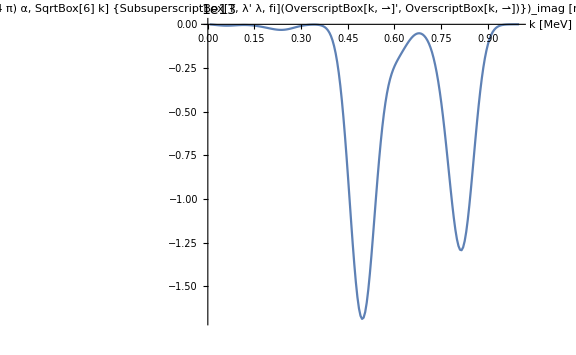

```mathematica
ImT[Mf_,Mi_,λf_,λi_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPList[[nJ,All]];
For[Mm=-Ll,Mm≤Ll,Mm++,(
For[Mmp=-Llp,Mmp≤Llp,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{Ll,Mm},{Llp,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{Llp,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]

kinfac=-(4 Pi)/(137 √6 kσ);
DissCross[Mf_,Mi_,λf_,λi_,θ_,kinfac_]:=kinfac Table[fit,{fit,ImT[Mf,Mi,λf,λi,θ]}];

ListPlot[Re[DissCross[Jf,Ji,1,0,0,kinfac]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`-FractionBox[(4  π) α, SqrtBox[6] k] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [mb]"}(*,Filling->cycl*),ImageSize->Large,Joined->True,DataRange->{Min[ks],Max[ks]}]
```

JbasisDim = {5,10,15,20,25,30}

Transpose::nmtx: The first two levels of {} cannot be transposed.

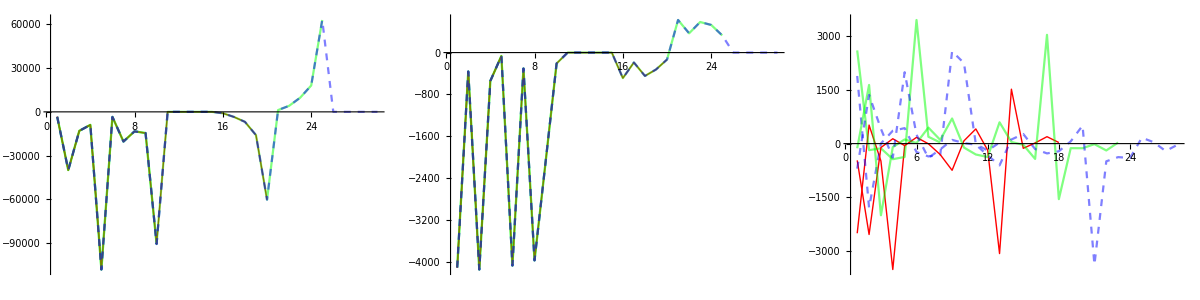

```mathematica
nJ=1;

lbd=basisdims[[nJ]][[1;;]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[#],Number]&/@lbd;
JbasisDim=NormHamMat[[All,1]];
norm=ArrayReshape[#[[2;;#[[1]]^2+1]],{#[[1]],#[[1]]}]&/@NormHamMat;
ham=ArrayReshape[#[[#[[1]]^2+2;;2 #[[1]]^2+1]],{#[[1]],#[[1]]}]&/@NormHamMat;
genevham=Sort[Eigenvalues[{ham[[#]],norm[[#]]}],Re[#1]>Re[#2]&]&/@Range[Length[JbasisDim]];
normev=Sort[Eigenvalues[#],Re[#1]>Re[#2]&]&/@norm;
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJs[[nJ]][[1]]]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[#]&/@JbasisDim;
Print["JbasisDim = ",JbasisDim];
inhomo=(*(2/mom)*) ReadList[#,Real,RecordLists->True][[momIndex]]&/@file;

renorm=DiagonalMatrix[1/Sqrt[Diagonal[#]]]&/@norm;
renormid=DiagonalMatrix[Table[1,{n,#}]]&/@JbasisDim;
hamre=renorm[[#]].ham[[#]].renorm[[#]]&/@Range[Length[JbasisDim]];

normre=renorm[[#]].norm[[#]].renorm[[#]]&/@Range[Length[JbasisDim]];
inhomore=renorm[[#]].inhomo[[#]]&/@Range[Length[JbasisDim]];
genevhamN=Eigenvalues[{hamre[[#]],normre[[#]]}]&/@Range[Length[JbasisDim]];
normevN=Sort[Eigenvalues[#],Re[#1]>Re[#2]&]&/@normre;

threshold=10^-1;
es=Eigensystem[norm[[#]]]&/@Range[Length[JbasisDim]];
μtransf=Transpose[Select[Sort[Transpose[es[[#]]],#1[[1]]<#2[[1]]&],#1[[1]]>threshold&]]&/@Range[Length[JbasisDim]];
μsOr=Transpose[Select[Sort[Transpose[es[[#]]],#1[[1]]<#2[[1]]&],#1[[1]]<=threshold&]]&/@Range[Length[JbasisDim]];
Oμ=(Transpose[μtransf[[#]][[2]]].DiagonalMatrix[(μtransf[[#]][[1]])^(-1/2)])&/@Range[Length[JbasisDim]];
λstrf=Eigensystem[(Transpose[Oμ[[#]]].ham[[#]]).Oμ[[#]]]&/@Range[Length[JbasisDim]];
inhomoCl=λstrf[[#]][[2]].(Transpose[Oμ[[#]]].inhomo[[#]])&/@Range[Length[JbasisDim]];

Grid[{{ListPlot[inhomo,Joined->True,PlotRange->Full,ImageSize->Large,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}],ListPlot[inhomore,Joined->True,PlotRange->Full,ImageSize->Large,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}],
ListPlot[inhomoCl,Joined->True,PlotRange->Full,ImageSize->Large,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}]}}]
```

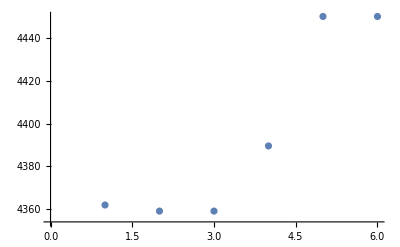

```mathematica
norminhom=Norm[inhomoCl[[#]]]&/@Range[Length[JbasisDim]];
ListPlot[norminhom]
```

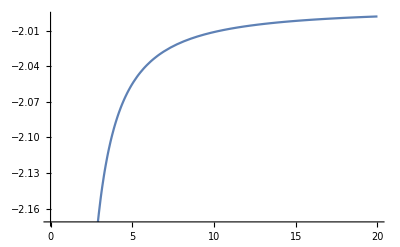

```mathematica
ff[t_,τ_]:=FunctionExpand[Integrate[(τ x)^-1 (x-τ)^(-3/2),x]/.x->t]
Plot[ff[t,1.2],{t,0,20},PlotRange->Automatic]
```

#### real part of the amplitude ( to be updated )

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_real=2π (-)^(L+I_f+I_i)L̂ L̂'  𝓅∫_E_0^∞ dE[(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i-k)+(-)^(L+L'+J)(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i+k')]

```mathematica
prefak=2 Pi (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp];
RePEoneJkernelAList=Table[ strengthfunctionList[[n]]/(ee-(e0+kkk)),{n,anzF}];
RePEoneJkernelBList=Table[(-1)^(Ll+Llp+Jj) strengthfunctionList[[n]]/(ee-(e0-kkk)),{n,anzF}];

gPAList=NIntegrate[RePEoneJkernelAList,{ee,e0,e0+kkk,Infinity},Method->"PrincipalValue"];
gPBList=NIntegrate[RePEoneJkernelBList,{ee,e0,e0-kkk,Infinity},Method->"PrincipalValue"];
genPolList=prefak (NIntegrate[RePEoneJkernelAList,{ee,e0,e0+kkk,Infinity},Method->"PrincipalValue"]+NIntegrate[RePEoneJkernelBList,{ee,e0,e0-kkk,Infinity},Method->"PrincipalValue"]);
(*
Plot[{RePEoneJkernelAList/.kkk->1,RePEoneJkernelBList/.kkk->1},{ee,emin,emax},PlotRange->Full,PlotLegends->{"F_((ν'L'νL)J)^I_f","(-)"},AxesLabel->{"E [MeV]",""},PlotStyle->{{Red,Dashed},{Blue,Dashed}},PlotLabel->"k="<>ToString[kkk]<>" MeV",ImageSize->Large]*)
```

Table::iterb: Iterator {n,anzF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {n,anzF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {n,anzF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
Plot[genPolList,{kkk,ks[[1]],ks[[-1]]},PlotRange->Full,PlotLegends->{"(∫^∞)_E_0dEF_((ν' L' νL) J)^I_f+(-)"},AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_real"},PlotPoints->10,ImageSize->Large]
```

Table::iterb: Iterator {n,anzF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NIntegrate::inumr: The integrand Table[({{0.,3.13396×10^9,1.38001×10^10,3.36032×10^10,6.35566×10^10,1.03865×10^11,1.53784×10^11,2.11581×10^11,2.74626×10^11,3.39589×10^11,4.0275×10^11,4.60367×10^11,5.09062×10^11,5.46179×10^11,5.70071×10^11,«21»,3.31613×10^12,3.77565×10^12,4.26326×10^12,4.77361×10^12,5.2991×10^12,5.82952×10^12,6.35188×10^12,6.85062×10^12,7.30813×10^12,7.70566×10^12,8.02456×10^12,8.24775×10^12,8.36125×10^12,8.35549×10^12,«151»},{«1»}}⟦n⟧)/(ee-(1.0758+kkk)),{n,anzF}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.0758,110.077}}.

NIntegrate::inumr: The integrand Table[({{0.,3.13396×10^9,1.38001×10^10,3.36032×10^10,6.35566×10^10,1.03865×10^11,1.53784×10^11,2.11581×10^11,2.74626×10^11,3.39589×10^11,4.0275×10^11,4.60367×10^11,5.09062×10^11,5.46179×10^11,5.70071×10^11,«21»,3.31613×10^12,3.77565×10^12,4.26326×10^12,4.77361×10^12,5.2991×10^12,5.82952×10^12,6.35188×10^12,6.85062×10^12,7.30813×10^12,7.70566×10^12,8.02456×10^12,8.24775×10^12,8.36125×10^12,8.35549×10^12,«151»},{«1»}}⟦n⟧)/(ee-(1.0758+kkk)),{n,anzF}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,112.077}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{gPAList,gPBList,genPolList},{kkk,ks[[1]],ks[[-1]]},PlotRange->Full,PlotLegends->{"(∫^∞)_E_0dEF_((ν' L' νL) J)^I_f","(∫^∞)_E_0dE(-)","Σ"},AxesLabel->{"k [MeV]","P_0"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},PlotPoints->10,ImageSize->Large]
```

Table::iterb: Iterator {n,anzF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NIntegrate::inumr: The integrand Table[({{0.,3.13396×10^9,1.38001×10^10,3.36032×10^10,6.35566×10^10,1.03865×10^11,1.53784×10^11,2.11581×10^11,2.74626×10^11,3.39589×10^11,4.0275×10^11,4.60367×10^11,5.09062×10^11,5.46179×10^11,5.70071×10^11,«21»,3.31613×10^12,3.77565×10^12,4.26326×10^12,4.77361×10^12,5.2991×10^12,5.82952×10^12,6.35188×10^12,6.85062×10^12,7.30813×10^12,7.70566×10^12,8.02456×10^12,8.24775×10^12,8.36125×10^12,8.35549×10^12,«151»},{«1»}}⟦n⟧)/(ee-(1.0758+kkk)),{n,anzF}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.0758,110.077}}.

NIntegrate::inumr: The integrand Table[({{0.,3.13396×10^9,1.38001×10^10,3.36032×10^10,6.35566×10^10,1.03865×10^11,1.53784×10^11,2.11581×10^11,2.74626×10^11,3.39589×10^11,4.0275×10^11,4.60367×10^11,5.09062×10^11,5.46179×10^11,5.70071×10^11,«21»,3.31613×10^12,3.77565×10^12,4.26326×10^12,4.77361×10^12,5.2991×10^12,5.82952×10^12,6.35188×10^12,6.85062×10^12,7.30813×10^12,7.70566×10^12,8.02456×10^12,8.24775×10^12,8.36125×10^12,8.35549×10^12,«151»},{«1»}}⟦n⟧)/(ee-(1.0758+kkk)),{n,anzF}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,112.077}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

analysis of individual expansion terms

```mathematica
compoLIT=List @@ plotlistLITs[[1]][[1]];
compoLITa=Accumulate[compoLIT];

compoRES=List @@ plotlistRESPONSEs[[1]][[1]];
compoRESa=Accumulate[compoRES];
nn=15;
Grid[{{Plot[compoLITa[[nn]],{x,0,50},PlotRange->Full,AxesLabel->{"σ [MeV]","L_j(σ) [fm^2 MeV^-2]"},
ImageSize->Large,LabelStyle->Directive[Larger],PlotLegends->"Expressions"],Plot[compoRESa[[nn]],{e,0,50},PlotRange->Full,AxesLabel->{"E [MeV]","F_j(E) [fm MeV^-2]"},
ImageSize->Large,LabelStyle->Directive[Larger],PlotLegends->"Expressions"]}}]
```

Part::partd: Part specification plotlistLITs⟦1⟧ is longer than depth of object.

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[plotlistLITs].

Part::partd: Part specification plotlistRESPONSEs⟦1⟧ is longer than depth of object.

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[plotlistRESPONSEs].

Part::partw: Part 15 of Accumulate[plotlistLITs] does not exist.

Part::partw: Part 15 of Accumulate[plotlistRESPONSEs] does not exist.

-Graphics- | -Graphics-

```mathematica
nJ=1;
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJs[[nJ]]]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
Print["JbasisDim = ",JbasisDim,"   :  ",file];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True];
```

JbasisDim = {5,10,15,20,25,30}   :  ./LIT_SOURCE_0.5^-_mJ{-0.5, 0.5}_MUL1_bv_1-{5, 10, 15, 20, 25, 30}

ReadList::noopen: Cannot open ./LIT_SOURCE_0.5^-_mJ{-0.5, 0.5}_MUL1_bv_1-{5, 10, 15, 20, 25, 30}.

```mathematica
kl=110;zk=13;ks=Table[kl+n,{n,0,12}];
ini=Table[inhomo[[All,n]]/ks,{n,3,5}];
ListPlot[ini,Joined->True,ImageSize->Large]
```

Part::partd: Part specification (2000. $Failed)⟦All,3⟧ is longer than depth of object.

Part::partd: Part specification (2000. $Failed)⟦All,4⟧ is longer than depth of object.

Part::partd: Part specification (2000. $Failed)⟦All,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Stop Evaluation here